Seeded QED cascades in counterpropagating laser pulses

T. Grismayer, M. Vranic, J. L. Martins, R. A. Fonseca, and L. O. Silva, Phys Rev E 95, 023210 (2017)
Notebook: Óscar Amaro, November 2022 @ GoLP-EPP
Contact: oscar.amaro@tecnico.ulisboa.pt

Introduction
In this notebook we reproduce some results from the paper.

## Setups A,B,C field components

```mathematica
(* setup 1 (lp-lp) *)
Clear[a0,k0,ω0,x,t,ap,am]
ap={0,a0 Cos[ω0 t+k0 x],0};
am={0,a0 Cos[ω0 t-k0 x],0};

(* E: only y component. pre-factor ω0 is due to choice of reduced units/normalization *)
Ε=-D[ap+am,t]//Simplify
(* B: only z component. pre-factor k0 is due to choice of reduced units/normalization *)
Β=Curl[ap+am,{x,y,z}]//Simplify
```

{0,2 a0 ω0 Cos[k0 x] Sin[t ω0],0}

{0,0,-2 a0 k0 Cos[t ω0] Sin[k0 x]}

```mathematica
(* setup 2 (cw-cw) *)
(*"...results in a helical field structure growing or shrinking uniformly in space..."*)
Clear[a0,k0,ω0,x,t,ap,am]
ap={0,a0 Cos[ω0 t+k0 x],a0 Sin[ω0 t+k0 x]};
am={0,a0 Cos[ω0 t-k0 x],-a0 Sin[ω0 t-k0 x]};

(* E: y+z components *)
Ε=-D[ap+am,t]//Simplify
(* B: y+z components *)
Β=Curl[ap+am,{x,y,z}]//Simplify
```

{0,2 a0 ω0 Cos[k0 x] Sin[t ω0],2 a0 ω0 Sin[k0 x] Sin[t ω0]}

{0,-2 a0 k0 Cos[k0 x] Cos[t ω0],-2 a0 k0 Cos[t ω0] Sin[k0 x]}

```mathematica
(* setup 3 (cw-cp) *)
(*"...fixed planar beating pattern that rotates around the laser propagation axis. This setup consists in a rotating field structure..."*)
Clear[a0,k0,ω0,x,t,ap,am]
ap={0,a0 Cos[ω0 t+k0 x],-a0 Sin[ω0 t+k0 x]};
am={0,a0 Cos[ω0 t-k0 x],-a0 Sin[ω0 t-k0 x]};

(* E: y+z components *)
Ε=-D[ap+am,t]//Simplify
(* B: y+z components *)
Β=Curl[ap+am,{x,y,z}]//Simplify
```

{0,2 a0 ω0 Cos[k0 x] Sin[t ω0],2 a0 ω0 Cos[k0 x] Cos[t ω0]}

{0,-2 a0 k0 Sin[k0 x] Sin[t ω0],-2 a0 k0 Cos[t ω0] Sin[k0 x]}

## A. Ideal model (check some of the calculations of the paper)

```mathematica
Clear[n0,s,t,Wγ,Wp,np,nptt,tt,intt,dnpdt]

(* invert Laplace transform of equation 6 *)
np=InverseLaplaceTransform[n0/(s-(2Wγ Wp)/(s+Wp)),s,t]//Simplify

(* LHS of eq 5 *)
dnpdt=D[np,t]//Simplify

(* change of variable *)
nptt=np/.{t->tt}//Simplify;
(* RHS of eq 5 *)
intt=2Integrate[nptt Wγ Wp Exp[-Wp(t-tt)],{tt,0,t}]//Simplify

(* check validity of eq 5 using Laplace transform of eq 6*)
Refine[intt-dnpdt//FullSimplify,{Wp>0,Wγ>0}]//Simplify
```

(ⅇ^(-1/2 t (Wp+√Wp √(Wp+8 Wγ))) n0 ((-1+ⅇ^(t √Wp √(Wp+8 Wγ))) √Wp+(1+ⅇ^(t √Wp √(Wp+8 Wγ))) √(Wp+8 Wγ)))/(2 √(Wp+8 Wγ))

(2 ⅇ^(-1/2 t (Wp+√Wp √(Wp+8 Wγ))) (-1+ⅇ^(t √Wp √(Wp+8 Wγ))) n0 √Wp Wγ)/(√(Wp+8 Wγ))

(4 ⅇ^(-(t Wp)/2) n0 √Wp Wγ Sinh[1/2 t √Wp √(Wp+8 Wγ)])/(√(Wp+8 Wγ))

0

{{s→-Wp/2-1/2 √(Wp (Wp+8 Wγ))},{s→1/2 (-Wp+√(Wp (Wp+8 Wγ)))}}

1/2 (-Wp+√(Wp (Wp+8 Wγ)))

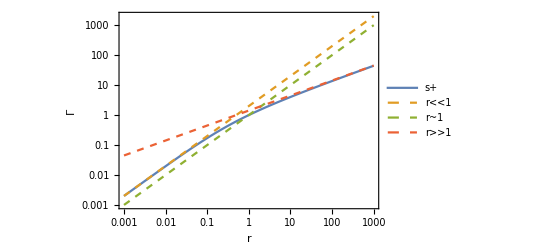

```mathematica
(* eqs 7 and 8 *)
Clear[sp,sm,s,Wp,Wγ,sol,r]
sol=Refine[Solve[s^2+Wp s-2 Wγ Wp==0,s],{Wp>0,Wγ>0}]//FullSimplify
sp=sol[[2,1,2]]

(* rescale *)
Wγ=r Wp;
Wp=1;

LogLogPlot[{sp,2Wγ,Wγ,Sqrt[2Wγ Wp]},{r,10^-3,10^3},PlotStyle->{Default,Dashed,Dashed,Dashed},PlotLegends->{"s+","r<<1","r~1","r>>1"},Frame->True,FrameLabel->{"r","Γ"}]
```

## III. CASCADE MODELS - Weak-field limit

```mathematica
Clear[Wp,d2Pdtdχγ,α,τc,χγ,ϵγ,χeavg,γavg,δ,f]
Clear[ℏ,m,c,e]
Clear[sols,argexp,dargexp,d2argexp]
Clear[fx0,d2fx0,hx0,int]

(* to get eq 11, just assume s+Wp ~ s in equation 10 and solve the quadratic equation s^2-2 ∫ ... = 0 *)

(* expressions in text after eq 10 *)
Wp=(3π)/50 α/τc Exp[-8/(3χγ)] χγ/ϵγ;
d2Pdtdχγ=Sqrt[2/(3π)] α/τc Exp[-δ]/(δ^(1/2)χeavg γavg);
δ=(2χγ)/(3χeavg(χeavg-χγ));

(* integrand of equation 11 *)
d2Pdtdχγ Wp//Simplify

(* "...the argument of the exponential possesses a unique maximum..."*)
argexp=-8/(3 χγ)-(2 χγ)/(3 χeavg^2-3 χeavg χγ);(* argument of exponential *)
dargexp=D[argexp,χγ]; (* derivative of this argument *)
d2argexp=D[argexp,{χγ,2}]//Simplify;(* second derivative of this argument *)
sols=Solve[dargexp==0,χγ](* get stationary points *)

d2argexp/.{χγ->sols[[1,1,2]]}(* 2 χeavg/3 is a maximum *)
d2argexp/.{χγ->sols[[2,1,2]]}(* 2 χeavg is a minimum *)
```

(3 ⅇ^(-8/(3 χγ)-(2 χγ)/(3 χeavg^2-3 χeavg χγ)) α^2 χγ)/(50 γavg ϵγ τc^2 χeavg √(χγ/(π χeavg^2-π χeavg χγ)))

{{χγ→(2 χeavg)/3},{χγ→2 χeavg}}

-54/χeavg^3

2/(3 χeavg^3)

```mathematica
(* physical derived constants *)
(*τc=ℏ/(m c^2);
α=e^2/(ℏ c);*)

(* text before eq 12 *) 
f=-δ-8/(3χγ)//Simplify
fx0=f/.{χγ->(2χeavg)/3}//Simplify
d2fx0=(D[f,{χγ,2}]//Simplify)/.{χγ->(2χeavg)/3}
hx0=Refine[1/Sqrt[δ]/.{χγ->(2χeavg)/3},{χeavg>0}]

(* apply Laplace method following text before eq 12 *)
int=Sqrt[(2π)/Abs[d2fx0]]hx0 Exp[fx0];

(* equation 12 for growth rate in weak-field limit. however, in the analysis in the text the pre-factors are removed from the Laplace method. We have to put them back *)
(* attention: ϵγ = γavg χγ/χeavg according to text before eq 10. *)
(* this then leads to eq 12 *)
Refine[Sqrt[(3π)/50 α/τc Sqrt[2/(3π)] α/τc 1/γavg^2 2 int]//Simplify,{χeavg>0,α>0,τc>0,γavg>0}]
```

(2 (-2 χeavg+χγ)^2)/(3 χeavg χγ (-χeavg+χγ))

-16/(3 χeavg)

-54/χeavg^3

(√3 √χeavg)/2

(ⅇ^(-8/3/χeavg) √π α χeavg)/(5 6^(1/4) γavg τc)